# Guess Mystery Mass

## Last Updated: 2026/01/12 v1.2.1

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

## User Input

```mathematica
(*bright ion mass*)
massDJ=40;
(*ion chain configuration*)
numBrightIons=1;
```

```mathematica
(*bright ion secular frequencies - axial, RF, EGGS*)
wsecList={705.8,1281.1,1541.6}*wkhz;
(*trap RF frequency*)
ωRF=19.0815*wmhz;
```

```mathematica
(*mystery mass search range*)
searchRange=Range[20,80,0.2];
```

```mathematica
(*known chain COM frequency*)
freqGuessMHz=0.766;
```

```mathematica
(*
mathieu solution order
(mathieuβOrder=1 gives the normal pseudopotential approximation)
warning: don't go above mathieuβOrder=4 b/c problems
*)
mathieuβOrder=4;
```

# General

## Import

```mathematica
(*memory management etc*)
Needs["Utilities`CleanSlate`"]
```

```mathematica
(*(*cleanup and return*)
Remove[resVar,tempVar];ClearSystemCache[];ClearInOut;*)
```

## Values

## Fundamental Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;
me=9.10938356*^-31;
qe=1.60217662*^-19;
c=2.99792458*^8;
kb=1.38064852*^-23;
```

```mathematica
(*derived*)
ke2=2.30707751*^-28;
a0=ℏ^2/me/ke2;
debye=1.*^-21/c;
amu=1.66053904*^-27;
```

## Units

```mathematica
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

```mathematica
{ns,us,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2π*{10.^3,10.^6,10.^9};
```

```mathematica
{mv,uv}={10.^-3,10.^-6};
```

## Options

## Messages

```mathematica
(*turn off messages*)
Evaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];
];
ParallelEvaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];
];
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,PlotRange->Automatic,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic(*,AspectRatio->Full*)];
SetOptions[ListPlot,PlotRange->Automatic,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic(*,AspectRatio->Full*)];
SetOptions[ListLinePlot,PlotRange->Automatic,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic(*,AspectRatio->Full*)];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Functions

## Mathieu Setup

```mathematica
(*recursion functions to define mathieu equations*)
Clear[D2n,recur];
D2n[n_]:=Block[{a,q,β},(a-(2*n-β)^2)/q];
recur[i_Integer,stop_Integer,dir:(-1|1)]:=1/(D2n[i*dir]-If[i≥stop,0,recur[i+1,stop,dir]]);
```

```mathematica
(*create recursive equation*)
Clear[GetBetaEQ];
GetBetaEQ[ordD_,ordAQ_]:=Block[{a,q,β,ϵ},
Normal[
Series[
a-q*(
recur[1,ordD+1,1]+recur[1,ordD+1,-1]
(*expand {a,q,β} perturbatively*)
)/.{a->ϵ*a,q->ϵ*q,β->ϵ*β},

(*expand the series in ϵ from orders [0,ordAQ+1]*)
{ϵ,0,ordAQ+1}
]
(*reduce perturbation terms*)
]/.{ϵ->1}
];
```

```mathematica
(*convenience solver function: solves mathieu analytically up to order ordD in the D matrix, and order ordAQ in {a,q} *)
Clear[SolveMathieu];
SolveMathieu[ordD_Integer,ordAQ_Integer]:=Block[{β},
β/.First@Solve[
β^2==GetBetaEQ[ordD,ordAQ],
β,
PositiveReals
]
][[1]];
```

## Helper Functions

```mathematica
(*get dimension (i.e. x, y, or z) of eigenvector for MotionalModes2 function*)
Clear[GetDimension];
GetDimension[vec_]:=First@Ordering[
Norm/@ArrayReshape[vec,{3,Length[vec]/3}],
-1];
```

## Motional Mode Calculation - 1

```mathematica
(*base motional mode calculation*)
Clear[MotionalModes];
MotionalModes[mArr_List,xyzFreq_List,λ3_:0.0,λ4_:0.0]:=Module[
{
chainFreq=Transpose[xyzFreq],
numIons=Length[mArr],
scaleArr=Sqrt[KroneckerProduct[mArr,1/mArr]]*(xyzFreq[[;;,3]]^2),
z0eq,z0eqArr,
L0EQlist,guessz0eq,L0Mn,L0MnMat,
VMatX,VMatY,VMatZ
},

(*set up objects for equilibrium positions*)
z0eqArr = Array[z0eq,numIons];
L0EQlist=(z0eqArr[[#]]+(1.5*λ3)*z0eqArr[[#]]^2+(2.*λ4)*z0eqArr[[#]]^3)==(
Sum[(z0eqArr[[#]] - z0eqArr[[k]])^-2,{k,1,#-1}] 
- Sum[(z0eqArr[[#]] - z0eqArr[[k]])^-2,{k, #+1,numIons}]
)&/@Range[numIons];
(*guess axial equilibrium positions*)
guessz0eq=Range[-#,#,(2*#)/(numIons-1)]&[numIons^(1/3)]//N;
guessz0eq=Transpose[Join[{z0eqArr},{guessz0eq}]];
z0eqArr=z0eqArr/.Chop[FindRoot[L0EQlist,guessz0eq]];

(*format axial equilibrium positions into usable format*)
L0Mn=Abs[Table[If[i==j,0,(z0eqArr[[i]]-z0eqArr[[j]])^-3],{i,numIons},{j,numIons}]];
L0MnMat=DiagonalMatrix[Total[L0Mn,{2}]]-L0Mn;

(*extract secular frequencies*)
VMatZ=scaleArr*(DiagonalMatrix[(1+(3.*λ3)*#+(6.*λ4)*#^2)&/@z0eqArr]+2*L0MnMat);
VMatY=scaleArr*(DiagonalMatrix[(chainFreq[[2,;;]]/chainFreq[[3,;;]])^2]-L0MnMat);
VMatX=scaleArr*(DiagonalMatrix[(chainFreq[[1,;;]]/chainFreq[[3,;;]])^2]-L0MnMat);

(*return secular frequencies in usable form*)
{Sqrt[#[[;;,1]]],#[[;;,2]]}&[{Eigensystem[VMatX],Eigensystem[VMatY],Eigensystem[VMatZ]}]
];
```

## Motional Mode Calculation - 2

```mathematica
(*this one accounts for stray fields but not anharmonicity*)
Clear[MotionalModes2];
MotionalModes2[mArr_List,xyzFreq_List,(*λ3_:0.0,λ4_:0.0,*)offsetArr_List:{0.,0.,0.}]:=Module[
{
numIons=Length[mArr],
chainFreq=Transpose[xyzFreq],
scaleArr=Sqrt[KroneckerProduct[mArr,1/mArr]]*(xyzFreq[[;;,3]]^2),
l0=(ke2/(mArr[[-1]]*amu*xyzFreq[[-1,-1]]^2))^(1/3),
guessr0eq,r0eq,r0eqArr,r0eqArrFinal,L0EQlist,
L0Mn,R0Mn,trapFreqMat,
idMat,L0Mn2,L0MnMix,L0MnSelf,L0MnFinal,
res
},

(*set up infra to guess equilibrium positions*)
r0eqArr = Array[r0eq,{3,numIons}];
guessr0eq=Join[ConstantArray[0.,{2,numIons}],{Range[-1.,1.,2./(numIons-1.)]*numIons^(1./3.)}];
guessr0eq=Flatten[{r0eqArr,guessr0eq},{{2,3},{1}}];
(*set up force balancing equations for equilibrium positions*)
L0EQlist=Table[
(r0eqArr[[dim,ion]])==(chainFreq[[3,ion]]/chainFreq[[dim,ion]])^2*(Sum[(r0eqArr[[dim,ion]] - r0eqArr[[dim,k]])/(Norm[r0eqArr[[;;,ion]] - r0eqArr[[;;,k]]])^3,{k,Delete[Range[numIons],ion]}] )
+qe/(l0*amu)*offsetArr[[dim]]/(mArr[[ion]]*chainFreq[[dim,ion]]^2),
{dim,3},
{ion,numIons}
];

(*guess equilibrium positions*)
r0eqArrFinal=r0eqArr/.Chop[FindRoot[Flatten[L0EQlist],guessr0eq]];
(*r0eqArrFinal=Transpose[(#-offsetArr)&/@Transpose[r0eqArrFinal]];*)
(*Print[r0eqArrFinal];*)

(*format equilibrium positions into usable format*)
(*get R0Mn = (R^ij)^-1*)
R0Mn=Table[If[i==j,0,
(Norm[r0eqArrFinal[[;;,i]] - r0eqArrFinal[[;;,j]]])^-1
],{i,numIons},{j,numIons}];
(*get L0Mn = Subscript[R, α]^ij*)
L0Mn=Table[If[i==j,0,
r0eqArrFinal[[dim,i]] - r0eqArrFinal[[dim,j]]],
{dim,3},{i,numIons},{j,numIons}];

(*calculate trap frequency matrix*)
trapFreqMat=Table[If[iDim==jDim,
DiagonalMatrix[(chainFreq[[iDim]]/chainFreq[[3]])^2],
ConstantArray[0.,{numIons,numIons}]
],{iDim,3},{jDim,3}];

(*calculate Subscript[B, ij]*)
idMat=Outer[Times,IdentityMatrix[3],ConstantArray[1.,{numIons,numIons}]-IdentityMatrix[numIons],2,1];
L0Mn2=Outer[R0Mn^2*#1*#2&,L0Mn,L0Mn,1];
L0MnMix=Map[R0Mn^3*#&,idMat-3.*L0Mn2,{2}];
L0MnSelf=Map[DiagonalMatrix,Total[-L0MnMix,{4}],{2}];
L0MnFinal=Map[#*scaleArr&,L0MnSelf+L0MnMix+trapFreqMat,{2}];
(*Print[Flatten[L0MnFinal/wmhz^2,{1}]//MatrixForm];*)

(*get eigenvalues and eigenvectors*)
res=Transpose[{Sqrt[#[[1]]],#[[2]]}]&[Eigensystem[Flatten[L0MnFinal,{{1,3},{2,4}}]]];
(*sort eigenvalues by dimension*)
Return[Flatten[
Values[GroupBy[res,GetDimension[#[[2]]]&]],
{{3},{1},{2}}
]];
];
```

# Calculate

## Generate Potential Parameters

## Extract Mass-Independent Mathieu Parameters

```mathematica
(*create arb order mathieu func*)
AbsoluteTiming[
βMathieuFunc[q_,a_]=Evaluate[SolveMathieu[mathieuβOrder+2,mathieuβOrder]];
]
```

{0.0227883,Null}

```mathematica
(*solve higher-order mathieu parameter eqn to get q and a parameters from measured secular freqs*)
{qx,ar,az}=Block[{qrDJ,arDJ,azDJ},
{qrDJ,arDJ,azDJ}/.First@NSolve[{
ωRF/2.*βMathieuFunc[0,2.*azDJ]==wsecList[[1]],(*axial*)
ωRF/2.*βMathieuFunc[qrDJ,-azDJ-arDJ]==wsecList[[2]],(*radial y (lower freq radial)*)
ωRF/2.*βMathieuFunc[qrDJ,-azDJ+arDJ]==wsecList[[3]],(*radial x (higher freq radial)*)
(*set limit for mathieu q*)
0.<qrDJ<0.9
},
{qrDJ,arDJ,azDJ}
]
];
```

```mathematica
(*make parameters mass-independent*)
{qx0,ar0,az0}=(massDJ)*{qx,ar,az};
```

### Old Style (Before 2026/01/12)

```mathematica
(*(*get mathieu parameters from known secular frequencies*)
(*Subscript[ω, x]=√(Subscript[q, x]^2/2-(Subscript[a, z]-Subscript[a, r])), Subscript[ω, y]=√(Subscript[q, x]^2/2-(Subscript[a, z]+Subscript[a, r])), Subscript[ω, z]=√(2*Subscript[a, z])*)
ar=1./(ωRF/2.)^2.*(wsecList[[3]]^2-wsecList[[2]]^2)/2.;(*Subscript[a, r]=(4*e*Subscript[V, 0])/(m*Subscript[r, 0]^2*Ω^2)*)
az=1./(ωRF/2.)^2. wsecList[[1]]^2/2;(*Subscript[a, z]=(8*e*Subscript[U, DC])/(m*Subscript[z, 0]^2*Ω^2)*)
qx=Sqrt[2(wsecList[[3]]^2/(ωRF/2)^2+(az-ar))];(*Subscript[q, r]=(2*e*Subscript[V, RF])/(m*Subscript[r, 0]^2*Ω^2)*)
*)
```

```mathematica
(*(*make parameters mass-independent*)
{qx0,ar0,az0}=(massDJ)*{qx,ar,az};*)
```

## Create Secular Frequency Functions for Arb. Mathieu Order

```mathematica
(*secular frequency calculations*)
Clear[ωSecRadial,ωSecAxial,ωSecXYZ];
ωSecRadial[q_,a_,β_]:=β/2.*βMathieuFunc[q,a];
ωSecAxial[a_,β_]:=β/2.*βMathieuFunc[0.,2.a];
ωSecXYZ[q_,ar_,az_,β_]:=β/2.*(βMathieuFunc@@@{{q,-(az-ar)},{q,-(az+ar)},{0.,2.*az}});
```

### Old Style (Before 2026/01/12)

```mathematica
(*(*secular frequency calculations*)
Clear[ωSecRadial,ωSecAxial,ωSecXYZ];
ωSecRadial[q_,a_,β_]:=β/2. Sqrt[q^2/2.-a];
ωSecAxial[a_,β_]:=β/2. Sqrt[2.*a];
ωSecXYZ[q_,ar_,az_,β_]:=β/2.*Sqrt[{q^2/2.-(az-ar),q^2/2.-(az+ar),2.*az}];*)
```

## Prepare Mode Parameters

```mathematica
(*convenience function to generate MotionalModes function input*)
mystParamsXYZ[massArr_]:={massArr,ωSecXYZ[qx0/#,ar0/#,az0/#,ωRF]&/@massArr};
```

```mathematica
(*create list of potential ion chain configurations*)
massArrList=Join[
{#},
ConstantArray[massDJ,numBrightIons]
]&/@searchRange;
(*massArrList=Join[ConstantArray[massDJ,numBrightIons],{#}]&/@searchRange;*)
(*massArrList={massDJ,#,massDJ}&/@searchRange;*)
```

```mathematica
(*create list of potential parameters for MotionalModes*)
paramArrXYZ=mystParamsXYZ/@massArrList;
```

## Get Potential Mode Frequencies

## Calculate Values

```mathematica
(*calculate!*)
(*guessRes axes are: mass, wmvals vs vmvals, direction, mode*)
AbsoluteTiming[
guessResXYZ=MotionalModes[##,0.]&@@@paramArrXYZ;
]
```

{0.0663224,Null}

```mathematica
(*create list of (x,y) for each direction and mode*)
resArrAll=Map[
Transpose[{searchRange,#}]&,
Flatten[guessResXYZ[[;;,1]],{{2},{3},{1}}]/wmhz,
{2}
];
(*extract only COM mode frequencies for x, y, and z, then format*)
{resArrX,resArrY,resArrZ}={resArrAll[[1,1]],resArrAll[[2,1]],resArrAll[[3,-1]]};
```

```mathematica
(*interpolate results*)
resInterpolateAll=Map[
Interpolation[#]&,
resArrAll,
{2}
];
(*separately get interpolation functions for each COM mode*)
{resInterpolX,resInterpolY,resInterpolZ}={resInterpolateAll[[1,1]],resInterpolateAll[[2,1]],resInterpolateAll[[3,-1]]};
```

## Guess Mass

```mathematica
(*guess the mass*)
massGuessAMU=x/.(
FindRoot[
#[x]==freqGuessMHz,
{x,massDJ}
]&/@{resInterpolX,resInterpolY,resInterpolZ}
);
```

```mathematica
(*create mode predict function*)
FrequencyPredict[mass_]:={resInterpolZ[mass],resInterpolY[mass],resInterpolX[mass]};
```

```mathematica
(*guess the mass - all modes*)
massGuessAMUall=x/.(
Map[
FindRoot[
#[x]==freqGuessMHz,
{x,massDJ}
]&,
resInterpolateAll,
{2}
]
);
```

## Create Figures

## Plots

```mathematica
(*plot all mode frequencies*)
resPlotSum=ListPlot[
{resArrX,resArrY,resArrZ},
PlotLabels->{"EGGS","RF","Axial"},
PlotRange->Automatic,
FrameLabel->{
 {Style["Frequency (COM, MHz)",{Black,Directive[15]}],None},
{Style["Mass (amu)",{Black,Directive[15]}],Style["Dark Ion Mass Candidates",{Black,Directive[15]}]}
}
];
```

```mathematica
(*separately plot for all dimensions*)
resPlots=MapThread[
ListPlot[
#1,
PlotRange->Automatic,
Joined->True,
FrameLabel->{
 {Style["Frequency (COM, MHz)",{Black,Directive[15]}],None},
{Style["Mass (amu)",{Black,Directive[15]}],
Style["Dark Ion Mass Candidates - "<>ToString[#2]<>" Mode",{Black,Directive[15]}]}
},
ImageSize->Scaled[0.3]
]&,
{
{resArrX,resArrY,resArrZ},
{"EGGS","RF","Axial"}
}
];
```

## Tables

#### Original

```mathematica
massTableData={
{NumberForm[#,{3,1}]},
{MatrixForm[{
resInterpolX[#],
resInterpolY[#],
resInterpolZ[#]
}]}
}&/@massGuessAMU;
```

```mathematica
(*format mass guess table*)
massTable=Style[
Labeled[
TableForm[
massTableData,
TableHeadings->{
{"EGGS","RF","Axial"},
{"Mass (AMU)","Mode Frequencies (MHz)"}
},
TableAlignments->{Right,Right}
],
"Dark Ion Candidates: ",
Top
],
Black,Background->White
];
```

```mathematica
(*create table of mode frequencies for typical masses*)
typicalResultsTable=Style[
Labeled[
TableForm[
{
FrequencyPredict[28],
FrequencyPredict[36],
FrequencyPredict[37],
FrequencyPredict[38],
FrequencyPredict[39]
},
TableHeadings->{
{"AMU 28","AMU 36","AMU 37","AMU 38","AMU 39"},
{"Axial COM","RF COM","EGGS COM"}
}
],
"Typical Masses",
Top
],
{
Background->White,
FontColor->Black,
ImageSize->Large,
Frame->True
}
];
```

#### New

```mathematica
GetAllModes[mass_]:=Map[
#[mass]&,
resInterpolateAll,
{2}
]//MatrixForm;
```

```mathematica
massTableDataAll=Map[
GetAllModes,
massGuessAMUall,
{2}
];
```

```mathematica
massTableAllHeadings=Outer[
#2<>""<>ToString[#1]&,
Range[IntegerPart[numBrightIons+2]],
{"EGGS","RF","Axial"}
];
```

```mathematica
(*format mass guess table - all modes*)
massTableAll=Style[
Labeled[
TableForm[
Transpose[
{Flatten[massGuessAMUall],
Flatten[massTableDataAll]}
],
TableHeadings->{
Flatten[massTableAllHeadings],
{"Mass (AMU)","Mode Frequencies (MHz)"}
},
TableAlignments->{Right,Right}
],
"Dark Ion Candidates: ",
Top
],
Black,Background->White
];
```

# Summary

```mathematica
massTableAll
```

| Mass (AMU) | Mode Frequencies (MHz)
EGGS1 | 304.993 | (0.766 | -12.0362
0.195604 | -40.6294
-1.86986 | -0.245414)
RF1 | 72.1907 | (1.46621 | 0.766
1.19185 | 0.424581
1.09838 | 0.58474)
Axial1 | 251.434 | (1.167 | -4.80416
0.766 | -18.4211
-0.169916 | 0.130184)
EGGS2 | 52.4683 | (1.4751 | 1.07318
1.20452 | 0.766
1.15269 | 0.653568)
RF2 | 188.959 | (1.39278 | -0.829479
1.08709 | -5.13704
0.766 | 0.348239)
Axial2 | 26.613 | (2.25273 | 1.44769
1.98438 | 1.16426
1.38095 | 0.766)Dark Ion Candidates:

```mathematica
(*guess COM mode frequencies for arbitrary mass*)
FrequencyPredict[28.]//MatrixForm
```

(0.759786
1.86767
2.13576)

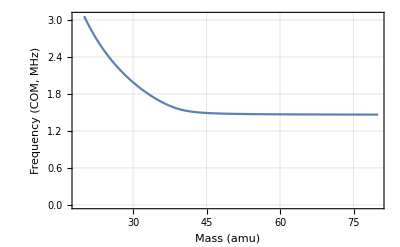
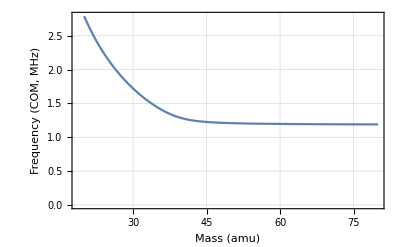
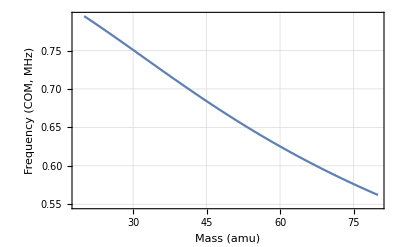
{{ | Mass (AMU) | Mode Frequencies (MHz)
EGGS | 305.0 | (0.766
0.195604
-0.245414)
RF | 251.0 | (1.167
0.766
0.130184)
Axial | 26.6 | (2.25273
1.98438
0.766)Dark Ion Candidates: , | Axial COM | RF COM | EGGS COM
AMU 28 | 0.759786 | 1.86767 | 2.13576
AMU 36 | 0.723636 | 1.39894 | 1.66283
AMU 37 | 0.719145 | 1.36176 | 1.62444
AMU 38 | 0.714674 | 1.32968 | 1.5912
AMU 39 | 0.710225 | 1.30284 | 1.56355Typical Masses},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{{massTable,typicalResultsTable},resPlots}
```

```mathematica
mystParamsXYZ[{40.,36.}]
```

{{40.,36.},{{9.68616×10^6,8.04939×10^6,4.43467×10^6},{1.07618×10^7,9.13062×10^6,4.67455×10^6}}}

```mathematica
(*get arbitrary mode values*)
arbModeVals=MotionalModes@@mystParamsXYZ[{40.,36.}];
arbModeVals[[1]]/wmhz//MatrixForm
```

(1.66283 | 1.42103
1.39894 | 1.12699
1.25685 | 0.723636)

# Deprecated